Construir uma caixa de comprimento de base 3 vezes maior que a largura da base. O material usado no topo e base custa 10/m^3 e o material usado nas laterais custa 6/m^3. A caixa deve ter volume 50 m^3. Determine as dimensões que minimizarão o custo para construir a caixa.

A área da base é x 3x=3 x^2.
A altura × base deve ser 50: 3 x^2 y=50.
Como y é um número, temos uma parábola em x ou grau -2 em y.
3 x^2=50/y⇒x=√(50/(3y)) e 
y=50/(3 x^2).

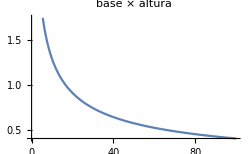
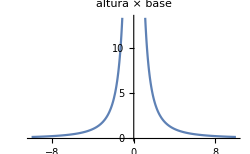

```mathematica
Row@{Plot[√(50/(3x)),{x,0,100},ImageSize->250,PlotLabel->"base × altura"],Plot[50/(3 x^2),{x,-10,10},ImageSize->250,PlotLabel->"altura × base"],Spacer@10}
```

Com o custo.

10x·10·3x·6y=50⇒
300x·6y=50⇒
{300x=50/(6y)⇒x=50/(1800y)
6y=50/(300x)⇒y=50/(1800x).

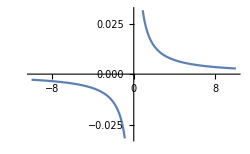

```mathematica
Plot[50/(1800x),{x,-10,10},ImageSize->250]
```

O que gera a parábola (e faz ser um problema de cálculo) é o fato de serem duas dimensões variáveis.

Uma empresa fabrica latas no formato cilíndrico circular reto com a capacidade de 500 cm3 de líquido. O material para a tampa e a base custa 0,02 unidades monetárias/cm2, enquanto que o material para a lateral custa 0,01 unidades monetárias/cm2. Desenvolva os seguintes itens no contexto de um processo de modelagem matemática:

(1) Expresse o Custo em função do raio da base da lata. Estime o raio r e a altura h da lata que tem o menor custo de fabricação.
(2) Suponha que a empresa faz a opção de que as duas partes da base e tampa são extraídas de folhas quadradas, cujos lados têm comprimento igual a 2r (r=raio da tampa e da base) e os retalhos são descartados. O que podemos afirmar em termos de custo sobre essa escolha da empresa? Vamos ter uma nova função custo? Se sim, qual é esta nova função custo?
Diante das condições dadas, estime o raio e altura da lata para o custo do item (2) para identificar a diferença.